```mathematica
SetDirectory[NotebookDirectory[]];
```

# h_scaling

## data

```mathematica
mpi=Flatten[Import["./LPAp_mpi/buffer/mPion.dat"]];

fpi=Flatten[Import["./LPAp_mub0/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub0/buffer/Zphi.dat"]];
h=Flatten[Import["./LPAp_mub0/buffer/c.dat"]]*197.33^3;
datamub0=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]/√Zphi[[2;;Length[h]]]]}];
h1mub0=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./LPAp_mub100/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub100/buffer/Zphi.dat"]];
h=Flatten[Import["./LPAp_mub100/buffer/c.dat"]]*197.33^3;
datamub100=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]/√Zphi[[2;;Length[h]]]]}];
h1mub100=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub100[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./LPAp_mub200/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub200/buffer/Zphi.dat"]];
h=Flatten[Import["./LPAp_mub200/buffer/c.dat"]]*197.33^3;
datamub200=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]/√Zphi[[2;;Length[h]]]]}];
h1mub200=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub200[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./LPAp_mub300/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub300/buffer/Zphi.dat"]];
h=Flatten[Import["./LPAp_mub300/buffer/c.dat"]]*197.33^3;
datamub300=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]/√Zphi[[2;;Length[h]]]]}];
h1mub300=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./LPAp_mub400/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub400/buffer/Zphi.dat"]];
h=Flatten[Import["./LPAp_mub400/buffer/c.dat"]]*197.33^3;
datamub400=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]/√Zphi[[2;;Length[h]]]]}];
h1mub400=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./LPAp_mub450/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub450/buffer/Zphi.dat"]];
h=Flatten[Import["./LPAp_mub450/buffer/c.dat"]]*197.33^3;
datamub450=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]/√Zphi[[2;;Length[h]]]]}];
h1mub450=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub450[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./LPAp_mub500/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub500/buffer/Zphi.dat"]];
h=Flatten[Import["./LPAp_mub500/buffer/c.dat"]]*197.33^3;
datamub500=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]/√Zphi[[2;;Length[h]]]]}];
h1mub500=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPAp_mub530/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub530/buffer/Zphi.dat"]];
h=Flatten[Import["./LPAp_mub530/buffer/c.dat"]]*197.33^3;
datamub530=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]/√Zphi[[2;;Length[h]]]]}];
h1mub530=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub530[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];

fpi=Flatten[Import["./LPAp_mub535/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub535/buffer/Zphi.dat"]];
h=Flatten[Import["./LPAp_mub535/buffer/c.dat"]]*197.33^3;
datamub535=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]/√Zphi[[2;;Length[h]]]]}];
h1mub535=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub535[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
```

## Plot

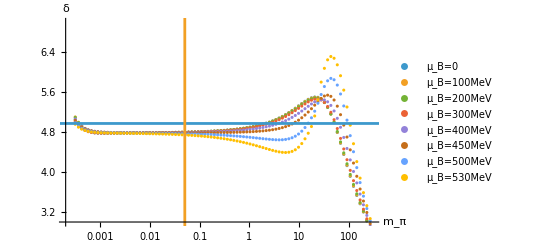

```mathematica
ploth=Show[ListPlot[{h1mub0,h1mub100,h1mub200,h1mub300,h1mub400,h1mub450,h1mub500,h1mub530(*,h1mub535*)},AxesLabel->{"m_π","δ"},PlotLegends->{"μ_B=0","μ_B=100MeV","μ_B=200MeV","μ_B=300MeV","μ_B=400MeV","μ_B=450MeV","μ_B=500MeV","μ_B=530MeV","μ_B=535MeV"},Axes->True,PlotRange->{{2 10^-4,300},{3,7}},ScalingFunctions->{"Log",Automatic}],ListLinePlot[{{{-20,4.975},{100,4.975}},{{Log[0.05],0},{Log[0.05],100}}}]]
```

```mathematica
Export["./LOdata/mub0.dat",h1mub0];
Export["./LOdata/mub100.dat",h1mub200];
Export["./LOdata/mub200.dat",h1mub200];
Export["./LOdata/mub300.dat",h1mub300];
Export["./LOdata/mub400.dat",h1mub400];
Export["./LOdata/mub450.dat",h1mub450];
Export["./LOdata/mub500.dat",h1mub500];
Export["./LOdata/mub530.dat",h1mub530];
Export["./LOdata/mub535.dat",h1mub535];
```